0.75+√(0.5625+ⅇ^(-50 (-0.5+y)^2))

(0.75+√(0.5625+ⅇ^(-50 (-0.5+y)^2)))^2

NIntegrate::precw: The precision of the argument function ((0.75  + √0.5625  + ⅇ^-50\ Plus[« 2 »]^2)^2
) is less than WorkingPrecision (24.).

2.70291816413668783474642

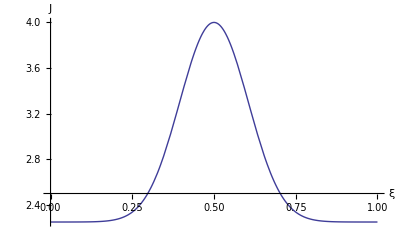

alg2_J.pdf

```mathematica
x=0.75;
u[x_,y_]=x+Sqrt[x^2+Exp[-50*(y-0.5)^2]]
J[x_,y_]=u[x,y]^2
mean=N[Integrate[J[x,y],{y,0,1}],14]
Plot[J[x,y],{y,0,1},PlotStyle->Thick,AxesLabel->{ξ,J}]
Export["alg2_J.pdf",%]
```